# Omicron analysis: Plotting partitioned case counts and Rt

## Splitting out lineage BA.1 / clade 21K from lineage BA.2 / clade 21L

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us-split

```mathematica
dataset="omicron-us-split";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
gridCount=4;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron 21K","Omicron 21L"};
```

```mathematica
n=Length[variants]
```

4

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.7,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8083415999999999, 0.7110806000000001, 0.255976],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01","2022-04-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Countries

```mathematica
countriesToDrop={};
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-11-01

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-02-20

```mathematica
countries=Union[seqData[[All,2]]]
```

{Arizona,California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Maryland,Massachusetts,Michigan,Minnesota,New Jersey,New York,North Carolina,Ohio,Pennsylvania,Rhode Island,Tennessee,Texas,Vermont,Washington,Wisconsin}

```mathematica
countries=Complement[countries,countriesToDrop]
```

{Arizona,California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Maryland,Massachusetts,Michigan,Minnesota,New Jersey,New York,North Carolina,Ohio,Pennsylvania,Rhode Island,Tennessee,Texas,Vermont,Washington,Wisconsin}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countryVariantCounts[country_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==country&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
countrySequenceCounts[country_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==country][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->countrySequenceCounts[#][[-15;;-1]]&,countries]
```

{Arizona→{{2022-02-06,95},{2022-02-07,189},{2022-02-08,285},{2022-02-09,260},{2022-02-10,213},{2022-02-11,157},{2022-02-12,90},{2022-02-13,67},{2022-02-14,114},{2022-02-15,118},{2022-02-16,97},{2022-02-17,82},{2022-02-18,37},{2022-02-19,29},{2022-02-20,0}},California→{{2022-02-06,1289},{2022-02-07,2487},{2022-02-08,2227},{2022-02-09,1940},{2022-02-10,1610},{2022-02-11,1342},{2022-02-12,1143},{2022-02-13,590},{2022-02-14,586},{2022-02-15,350},{2022-02-16,211},{2022-02-17,156},{2022-02-18,5},{2022-02-19,0},{2022-02-20,0}},Colorado→{{2022-02-06,195},{2022-02-07,556},{2022-02-08,379},{2022-02-09,322},{2022-02-10,298},{2022-02-11,163},{2022-02-12,38},{2022-02-13,21},{2022-02-14,48},{2022-02-15,14},{2022-02-16,15},{2022-02-17,14},{2022-02-18,0},{2022-02-19,0},{2022-02-20,0}},Connecticut→{{2022-02-06,75},{2022-02-07,101},{2022-02-08,99},{2022-02-09,87},{2022-02-10,93},{2022-02-11,70},{2022-02-12,41},{2022-02-13,50},{2022-02-14,155},{2022-02-15,133},{2022-02-16,25},{2022-02-17,33},{2022-02-18,13},{2022-02-19,8},{2022-02-20,3}},Florida→{{2022-02-06,284},{2022-02-07,483},{2022-02-08,392},{2022-02-09,383},{2022-02-10,193},{2022-02-11,199},{2022-02-12,250},{2022-02-13,192},{2022-02-14,109},{2022-02-15,135},{2022-02-16,111},{2022-02-17,74},{2022-02-18,1},{2022-02-19,0},{2022-02-20,0}},Georgia→{{2022-02-06,84},{2022-02-07,187},{2022-02-08,145},{2022-02-09,130},{2022-02-10,55},{2022-02-11,86},{2022-02-12,76},{2022-02-13,47},{2022-02-14,40},{2022-02-15,36},{2022-02-16,38},{2022-02-17,9},{2022-02-18,0},{2022-02-19,0},{2022-02-20,0}},Illinois→{{2022-02-06,91},{2022-02-07,119},{2022-02-08,151},{2022-02-09,156},{2022-02-10,164},{2022-02-11,130},{2022-02-12,111},{2022-02-13,95},{2022-02-14,122},{2022-02-15,75},{2022-02-16,66},{2022-02-17,19},{2022-02-18,2},{2022-02-19,1},{2022-02-20,0}},Indiana→{{2022-02-06,23},{2022-02-07,184},{2022-02-08,86},{2022-02-09,87},{2022-02-10,32},{2022-02-11,47},{2022-02-12,33},{2022-02-13,32},{2022-02-14,21},{2022-02-15,27},{2022-02-16,25},{2022-02-17,16},{2022-02-18,10},{2022-02-19,1},{2022-02-20,5}},Maryland→{{2022-02-06,52},{2022-02-07,121},{2022-02-08,51},{2022-02-09,51},{2022-02-10,53},{2022-02-11,33},{2022-02-12,41},{2022-02-13,19},{2022-02-14,22},{2022-02-15,19},{2022-02-16,12},{2022-02-17,15},{2022-02-18,3},{2022-02-19,2},{2022-02-20,0}},Massachusetts→{{2022-02-06,427},{2022-02-07,779},{2022-02-08,472},{2022-02-09,517},{2022-02-10,354},{2022-02-11,244},{2022-02-12,260},{2022-02-13,218},{2022-02-14,520},{2022-02-15,386},{2022-02-16,25},{2022-02-17,25},{2022-02-18,1},{2022-02-19,0},{2022-02-20,0}},Michigan→{{2022-02-06,51},{2022-02-07,126},{2022-02-08,118},{2022-02-09,117},{2022-02-10,101},{2022-02-11,53},{2022-02-12,75},{2022-02-13,43},{2022-02-14,62},{2022-02-15,51},{2022-02-16,41},{2022-02-17,24},{2022-02-18,1},{2022-02-19,0},{2022-02-20,0}},Minnesota→{{2022-02-06,210},{2022-02-07,380},{2022-02-08,314},{2022-02-09,287},{2022-02-10,240},{2022-02-11,223},{2022-02-12,131},{2022-02-13,92},{2022-02-14,121},{2022-02-15,180},{2022-02-16,155},{2022-02-17,115},{2022-02-18,72},{2022-02-19,28},{2022-02-20,0}},New Jersey→{{2022-02-06,80},{2022-02-07,47},{2022-02-08,88},{2022-02-09,122},{2022-02-10,125},{2022-02-11,55},{2022-02-12,70},{2022-02-13,36},{2022-02-14,26},{2022-02-15,30},{2022-02-16,23},{2022-02-17,46},{2022-02-18,34},{2022-02-19,9},{2022-02-20,0}},New York→{{2022-02-06,136},{2022-02-07,178},{2022-02-08,241},{2022-02-09,189},{2022-02-10,183},{2022-02-11,125},{2022-02-12,110},{2022-02-13,85},{2022-02-14,157},{2022-02-15,41},{2022-02-16,57},{2022-02-17,78},{2022-02-18,52},{2022-02-19,8},{2022-02-20,0}},North Carolina→{{2022-02-06,159},{2022-02-07,271},{2022-02-08,335},{2022-02-09,302},{2022-02-10,377},{2022-02-11,398},{2022-02-12,196},{2022-02-13,101},{2022-02-14,172},{2022-02-15,90},{2022-02-16,111},{2022-02-17,88},{2022-02-18,32},{2022-02-19,11},{2022-02-20,7}},Ohio→{{2022-02-06,51},{2022-02-07,164},{2022-02-08,115},{2022-02-09,79},{2022-02-10,60},{2022-02-11,38},{2022-02-12,19},{2022-02-13,19},{2022-02-14,20},{2022-02-15,21},{2022-02-16,20},{2022-02-17,16},{2022-02-18,3},{2022-02-19,1},{2022-02-20,0}},Pennsylvania→{{2022-02-06,53},{2022-02-07,135},{2022-02-08,163},{2022-02-09,160},{2022-02-10,112},{2022-02-11,56},{2022-02-12,56},{2022-02-13,21},{2022-02-14,30},{2022-02-15,47},{2022-02-16,21},{2022-02-17,22},{2022-02-18,0},{2022-02-19,6},{2022-02-20,0}},Rhode Island→{{2022-02-06,27},{2022-02-07,53},{2022-02-08,49},{2022-02-09,72},{2022-02-10,39},{2022-02-11,20},{2022-02-12,5},{2022-02-13,7},{2022-02-14,33},{2022-02-15,10},{2022-02-16,6},{2022-02-17,6},{2022-02-18,0},{2022-02-19,0},{2022-02-20,0}},Tennessee→{{2022-02-06,160},{2022-02-07,235},{2022-02-08,283},{2022-02-09,99},{2022-02-10,100},{2022-02-11,83},{2022-02-12,64},{2022-02-13,64},{2022-02-14,50},{2022-02-15,71},{2022-02-16,55},{2022-02-17,29},{2022-02-18,4},{2022-02-19,0},{2022-02-20,0}},Texas→{{2022-02-06,257},{2022-02-07,348},{2022-02-08,450},{2022-02-09,327},{2022-02-10,310},{2022-02-11,304},{2022-02-12,199},{2022-02-13,124},{2022-02-14,152},{2022-02-15,88},{2022-02-16,85},{2022-02-17,54},{2022-02-18,7},{2022-02-19,3},{2022-02-20,1}},Vermont→{{2022-02-06,57},{2022-02-07,191},{2022-02-08,160},{2022-02-09,75},{2022-02-10,128},{2022-02-11,49},{2022-02-12,67},{2022-02-13,34},{2022-02-14,206},{2022-02-15,15},{2022-02-16,2},{2022-02-17,0},{2022-02-18,0},{2022-02-19,0},{2022-02-20,0}},Washington→{{2022-02-06,44},{2022-02-07,152},{2022-02-08,240},{2022-02-09,190},{2022-02-10,215},{2022-02-11,69},{2022-02-12,33},{2022-02-13,24},{2022-02-14,134},{2022-02-15,83},{2022-02-16,67},{2022-02-17,0},{2022-02-18,0},{2022-02-19,1},{2022-02-20,0}},Wisconsin→{{2022-02-06,80},{2022-02-07,96},{2022-02-08,129},{2022-02-09,123},{2022-02-10,105},{2022-02-11,92},{2022-02-12,64},{2022-02-13,71},{2022-02-14,104},{2022-02-15,89},{2022-02-16,29},{2022-02-17,24},{2022-02-18,28},{2022-02-19,7},{2022-02-20,0}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[country_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==country,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.00001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[4]]],PlotRange->{logitTransform[0.0005],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[4]]],PlotRange->{0,If[maxFreq>0.95,1,maxFreq]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[country_]:=Map[logisticPrevSeries[countryVariantCounts[country,#],countrySequenceCounts[country]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForCountries=Map[freqForCountry,countries];
```

```mathematica
modeledFreqsForCountries=Map[{modeledLogisticPrevSeries[logisticPrevSeries[countryVariantCounts[#,"Omicron 21L"],countrySequenceCounts[#]]]}&,countries];
```

```mathematica
legendsForCountries=Map[constructGrowthRateLegend[modeledGrowthRate[#[[4]]],variants[[4]],legendStartingPointY- 0.09,colors[[4]]]&,freqsForCountries];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-us-split_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-us-split_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[country_,variant_]:=Module[{countryVariantFrequencyDateSeries,countryCasesDateSeries,tuples},
countryVariantFrequencyDateSeries=smoothedPrevalence[countryVariantCounts[country,variant],countrySequenceCounts[country]];
countryCasesDateSeries=csGather[country];
tuples=compareWithDate[countryVariantFrequencyDateSeries,countryCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
panels=Map[splitCasePlot,countries];
```

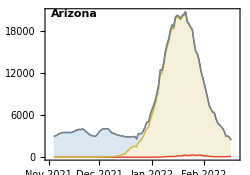
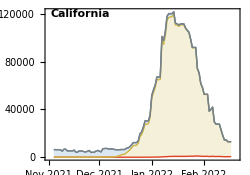
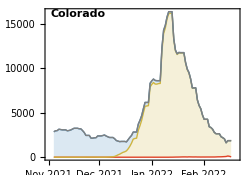
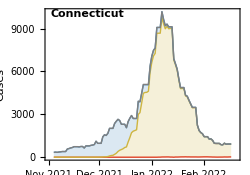
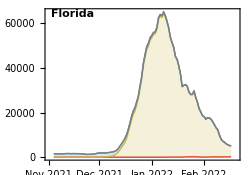
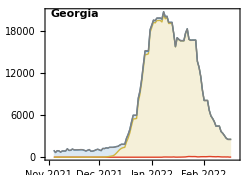
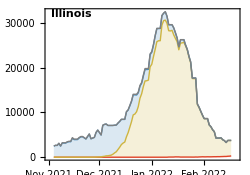
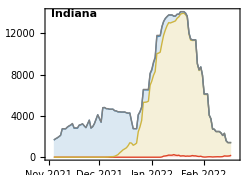
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us-split_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=500000;
```

```mathematica
splitCaseLogPlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[country_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[country_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[country,"Omicron 21L"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->200,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{50,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[4]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.88,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForCountries=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron 21L"]],"Omicron 21L",legendStartingPointY- 0.09,colors[[4]]]&,countries];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{countries,legendsForCountries}];
```

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us-split_partitioned-log-cases.png